# For Beginners: Lists

```mathematica
{1,3,4}
```

{1,3,4}

```mathematica
{1, a, cat, CurrentImage[]}
```

{1,a,cat,-Graphics-}

```mathematica
mylist = {1, a, cay}
```

{1,a,cay}

```mathematica
mylist+1
```

{2,1+a,1+cay}

```mathematica
Range[3,8]
```

{3,4,5,6,7,8}

```mathematica
mylist[[3]]
```

cay

```mathematica
Range[8]
```

{1,2,3,4,5,6,7,8}

```mathematica
Table[j,{j,1,8}]
```

{1,2,3,4,5,6,7,8}

```mathematica
Table[i, {i,1,8,2}]
```

{1,3,5,7}

```mathematica
Table[i, {i, 1, 8, 0.2}]
```

{1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.,5.2,5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.}

```mathematica
discerolls = RandomInteger[{1,8}, 10]
```

{3,8,2,8,4,5,6,3,3,4}

```mathematica
1.0 * Mean[discerolls]
```

4.49988

```mathematica
discerolls = RandomInteger[{1,8}, 10000000];
```

```mathematica
squares = Table[i^2, {i, 1, 8}]
```

{1,4,9,16,25,36,49,64}

```mathematica
upto8 = Range[8]
```

{1,2,3,4,5,6,7,8}

```mathematica
Map[f, {a, b, c}]
```

{f[a],f[b],f[c]}

```mathematica
apply function to square
```

```mathematica
Map[#^2 &, upto8]
```

{1,4,9,16,25,36,49,64}

```mathematica
Map[Sqrt[#] &, {1,4,9,16,25,36,49,64}]
```

{1,2,3,4,5,6,7,8}

Visualizing list

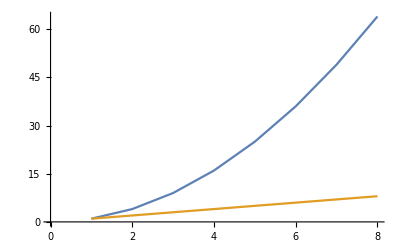

```mathematica
ListPlot[{squares, upto8}, Joined->True]
```

```mathematica
Length[squares]
```

8

```mathematica
NestList[f, a,5]
```

{a,f[a],f[f[a]],f[f[f[a]]],f[f[f[f[a]]]],f[f[f[f[f[a]]]]]}

```mathematica
NestList[# *2 &, 1, 5]
```

{1,2,4,8,16,32}

```mathematica
NestList[# ^2 &, 2, 10]
```

{2,4,16,256,65536,4294967296,18446744073709551616,340282366920938463463374607431768211456,115792089237316195423570985008687907853269984665640564039457584007913129639936,13407807929942597099574024998205846127479365820592393377723561443721764030073546976801874298166903427690031858186486050853753882811946569946433649006084096,179769313486231590772930519078902473361797697894230657273430081157732675805500963132708477322407536021120113879871393357658789768814416622492847430639474124377767893424865485276302219601246094119453082952085005768838150682342462881473913110540827237163350510684586298239947245938479716304835356329624224137216}

```mathematica
NestWhileList[# *2 &, 1, #≤129 &]
```

{1,2,4,8,16,32,64,128,256}

```mathematica
{1,2,3} + {a, b, c}
```

{1+a,2+b,3+c}

Sets

```mathematica
Union[{1,2,3},{3,4}]
```

{1,2,3,4}

```mathematica
Intersection[{1,2,3,4},{2,3}]
```

{2,3}

```mathematica
Subsets[{1,2,3}]
```

{{},{1},{2},{3},{1,2},{1,3},{2,3},{1,2,3}}

```mathematica
Join[{1,2}, {2,1}]
```

{1,2,2,1}

```mathematica
Riffle[{1,2},{a,b}]
```

{1,a,2,b}

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Take[{1,2,3,4,5,6,7,8,9,10},3]
```

{1,2,3}

```mathematica
Drop[{1,2,3,4,5,6,7,8,9,10},3]
```

{4,5,6,7,8,9,10}

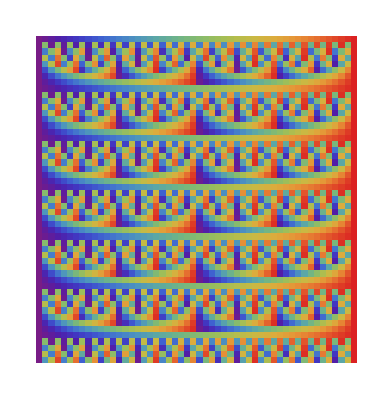

```mathematica
ArrayPlot[NestList[Riffle[Take[#,26], Drop[#, 26]] &, Range[52], 52], ColorFunction->"Rainbow"]
```

Matrix

```mathematica
MatrixForm[{{1,2},{3,4}}]
```

(1 | 2
3 | 4)

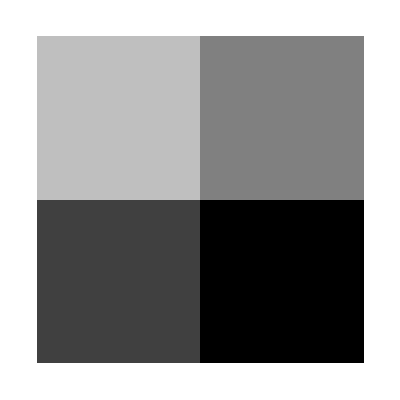

```mathematica
ArrayPlot[{{1,2},{3,4}}]
```

Functions

```mathematica
Sqrt[4]
```

2

```mathematica
timestwoadd[x_] := 2*x+1
```

```mathematica
timestwoadd[7]
```

15

```mathematica
fn := #*2+1 &
```

```mathematica
fn[7]
```

15

most useful functions

```mathematica
testifinputis7[wat_] := If[wat ==7, 1, 0]
```

```mathematica
testifinputis7[7.0111]
```

0

```mathematica
testifinputis7[7]
```

1

```mathematica
Map[testifinputis7, Range[10]]
```

{0,0,0,0,0,0,1,0,0,0}

```mathematica
If[4>2, 1, 0]
```

1

```mathematica
Map[{#, Mod[#, 5]} &, Range[30]]
```

{{1,1},{2,2},{3,3},{4,4},{5,0},{6,1},{7,2},{8,3},{9,4},{10,0},{11,1},{12,2},{13,3},{14,4},{15,0},{16,1},{17,2},{18,3},{19,4},{20,0},{21,1},{22,2},{23,3},{24,4},{25,0},{26,1},{27,2},{28,3},{29,4},{30,0}}

```mathematica
Map[{#, Mod[#,5]} &, Range[30]]
```

{{1,1},{2,2},{3,3},{4,4},{5,0},{6,1},{7,2},{8,3},{9,4},{10,0},{11,1},{12,2},{13,3},{14,4},{15,0},{16,1},{17,2},{18,3},{19,4},{20,0},{21,1},{22,2},{23,3},{24,4},{25,0},{26,1},{27,2},{28,3},{29,4},{30,0}}

```mathematica
collatz[x_,y_] := If[x==3*y||x==2*y+1||y==3*x||y==2*x+1, 1, 0]
```

```mathematica
Array[# &, 10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Array[#^2 &, 10]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Array[#^2 &, {2,3}]
```

{{1,1,1},{4,4,4}}

```mathematica
MatrixForm[Array[#^2 &, {4,4}]]
```

(1 | 1 | 1 | 1
4 | 4 | 4 | 4
9 | 9 | 9 | 9
16 | 16 | 16 | 16)

### ? & #

```mathematica
MatrixForm[Array[#1 +2 #2 &, {4,4}]]
```

(3 | 5 | 7 | 9
4 | 6 | 8 | 10
5 | 7 | 9 | 11
6 | 8 | 10 | 12)

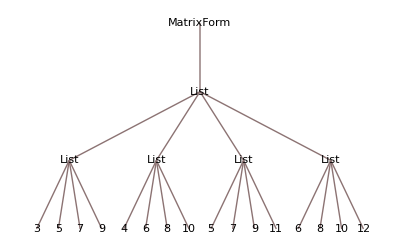

```mathematica
TreeForm[MatrixForm[Array[#1 +2 #2 &, {4,4}]]]
```

```mathematica
Array[collatz[#1, #2] &, {20, 20}]
```

{{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
AdjacencyGraph[Array[collatz[#1, #2] &, {50, 50}]]
```

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
GraphPlot3D[AdjacencyGraph[Array[collatz[#1, #2] &, {150, 150}]]]
```

-Graphics3D-

```mathematica
Position[Map[Mod[#, 7] &, Range[100]],6]
```

{{6},{13},{20},{27},{34},{41},{48},{55},{62},{69},{76},{83},{90},{97}}

```mathematica
Map[#[[1]] &, Position[Map[Mod[#, 7] &, Range[100]],6]]
```

{6,13,20,27,34,41,48,55,62,69,76,83,90,97}

```mathematica
Flatten[{{6},{13},{20},{27},{34},{41},{48},{55},{62},{69},{76},{83},{90},{97}}]
```

{6,13,20,27,34,41,48,55,62,69,76,83,90,97}

```mathematica
Select[Table[i, {i,1,10}], Mod[#, 3] ==0 &]
```

{3,6,9}

```mathematica
Table[i, {i,1,10}]
```

{1,2,3,4,5,6,7,8,9,10}

### ?

```mathematica
Sort[RandomReal[{0,1},7],#1≥ #2 &]
```

{0.922562,0.867024,0.503513,0.346391,0.256658,0.171953,0.168375}

## Strings

```mathematica
"mystring"
```

mystring

```mathematica
StringJoin["dog", "fish"]
```

dogfish

```mathematica
FullForm[{1,2,3}]
```

List[1,2,3]

```mathematica
FullForm[#]
```

Slot[1]

```mathematica
ToString[{1,2,3,4,5,6,7,8,9,10}]
```

{1, 2, 3, 4, 5, 6, 7, 8, 9, 10}

```mathematica
ToExpression["{1,2,3,4,5,6,7,8,9,10}"]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
StringSplit["{1,2,3,4,5,6,7,8,9,10}", "1"]
```

{{,,2,3,4,5,6,7,8,9,,0}}

```mathematica
Characters["catfish"]
```

{c,a,t,f,i,s,h}

```mathematica
NestList[StringReplace[#, "110"-> "100011101"] &, "110110110", 5]
```

{110110110,100011101100011101100011101,100011000111011000111010011000111011000111010011000111011,100010001110100110001110110001110100110001110110010001110100110001110110001110100110001110110010001110100110001110111,100010001100011101100100011101001100011101100011101001100011101100100011101001100011101100011101010001100011101100100011101001100011101100011101001100011101100100011101001100011101100011101010001100011101100100011101001100011101111,100010001000111010011000111011000111010100011000111011001000111010011000111011000111010011000111011001000111010011000111011000111010100011000111011001000111010011000111011000111010011000111011010001000111010011000111011000111010100011000111011001000111010011000111011000111010011000111011001000111010011000111011000111010100011000111011001000111010011000111011000111010011000111011010001000111010011000111011000111010100011000111011001000111010011000111011111}

```mathematica
conv[x_] := Map[If[# == "0", 1, 2] &, Characters[x]]
```

```mathematica
conv["110110110"]
```

{2,2,1,2,2,1,2,2,1}